```mathematica
NotebookEvaluate["https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/2020_aerosol-wind-instruments/00_SplinePack-034.nb"]  // Quiet;

Get[URLDownload["https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/2020_aerosol-wind-instruments/TP_ImProc_01-m101.wl"]] //Quiet;

Get[URLDownload["https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/2020_aerosol-wind-instruments/TP_ImProc_01-m101.wl"]] //Quiet;



Clear[SavitzkyGolayFilterExtended]


SavitzkyGolayFilterExtended[DOrder_,M_,nl_,nr_,data_] := Module[{i,j,p,t},
p = Table[t^i,{i,0,M}];
j = nl+nr+1;
i = Range[j];
Join[
D[Fit[Transpose[{i,Take[data,   j]}],p,t],{t,DOrder}]/.t->Take[i,  nl],
SavitzkyGolayFilter[DOrder,M,nl,nr,data],
D[Fit[Transpose[{i,Take[data,-j]}],p,t],{t,DOrder}]/.t->Take[i,-nr]]];



Clear[
ParamPadToTake,
ParamTakeToPad]


ParamPadToTake[ImgDim_,LeftRightBottomTop_] := {
{LeftRightBottomTop[[2,2]]+1,If[ListQ[ImgDim],ImgDim[[2]],-1]-LeftRightBottomTop[[2,1]]},
{LeftRightBottomTop[[1,1]]+1,If[ListQ[ImgDim],ImgDim[[1]],-1]-LeftRightBottomTop[[1,2]]}};


ParamTakeToPad[ImgDim_,RowsCols_] := Module[{LeftRightBottomTop},
LeftRightBottomTop = Reverse[RowsCols];
LeftRightBottomTop = Transpose[LeftRightBottomTop];
LeftRightBottomTop[[1]] -= 1;
LeftRightBottomTop[[2]] = ImgDim-LeftRightBottomTop[[2]];
LeftRightBottomTop = Transpose[LeftRightBottomTop];
LeftRightBottomTop[[2]] = Reverse[LeftRightBottomTop[[2]]];
LeftRightBottomTop];



Clear[
LoadFromTIF,
SaveAsTIF]


LoadFromTIF[CheckBitLength_,fname_] := Module[{X},
X = Import[fname];
X[[-1]] = ReadQRCode[X[[-1]]];
If[
If[TrueQ[CheckBitLength],
SameQ[
Piecewise[{{1,#≤1},{8,1<#≤8}},16]&/@Ceiling[Log[2,X[[-1,1]]]],
Ceiling[Log[2,Map[Length[Union@@ImageData[#]]&,Drop[X,-1]]]]],
True],
X[[-1]] = X[[-1,2]];
Fold[
ReplacePart[#1,#2[[1]],#2[[2]]]&,
X[[-1]],
Transpose[
{Drop[X,-1],
Position[X[[-1]],Image]}]]]];


SaveAsTIF[fname_,data_] := Module[{x,X},
X = data/.x_:>MyVectorPlaceholder/;ImageQ[x];
X = Append[
Extract[data,Position[X,MyVectorPlaceholder]],
X/.MyVectorPlaceholder->Image];
X[[-1]] = {Map[Length[Union@@ImageData[#]]&,Drop[X,-1]],X[[-1]]};
X[[-1]] = WriteQRCode[X[[-1]]];
MDExport[fname,X,"ImageEncoding"->"LZW"]];



Clear[ChangeImgDims]


ChangeImgDims[
  B_?ImageQ,
nx_?IntegerQ,
ny_?IntegerQ,
padding_] := Module[{R,x,y},
{x,y} = {nx,ny}-ImageDimensions[R=B];
If[y<0,
y = {Quotient[-y,2],-y};
y = {First[y],Subtract@@y}+{1,-1};
R = ImageTake[R,y],
If[y>0,
y = {y,Quotient[y,2]};
y = {Last[y],Subtract@@y};
R = ImagePad[R,{{0,0},y},padding]]];
If[x<0,
x = {Quotient[-x,2],-x};
x = {First[x],Subtract@@x}+{1,-1};
R = ImageTake[R,All,x],
If[x>0,
x = {x,Quotient[x,2]};
x = {Last[x],Subtract@@x};
R = ImagePad[R,{x,{0,0}},padding]]];
R];
```

Null[[3]].Null[[2]].Null[[1]] Null[[4]]:Null[[5]]:Null[[6]]    (FileByteCount[] Bytes)

Null[[3]].Null[[2]].Null[[1]] Null[[4]]:Null[[5]]:Null[[6]]    (FileByteCount[] Bytes)

Null[[3]].Null[[2]].Null[[1]] Null[[4]]:Null[[5]]:Null[[6]]    (FileByteCount[] Bytes)

```mathematica
$HistoryLength = 10;
```

```mathematica
PrependTo[MyTS,FontSize->18];
```

```mathematica
QubusVolume = 19.9;
```

```mathematica
Clear[ToEnglish]
ToEnglish = First[Get["https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/2020_aerosol-wind-instruments/EmissionRatePlotData.dat"]]
```

{Kl→C,Kl02→C2,Tr→T,Tr01→T1,Ob→O,Ob02→O2,Ob03→O3,Ob04→O4,Ob05→O5,Ob06→O6,Ob07→O7,Ob08→O8,Ob09→O9,Ob10→O10,Ob11→O11,Ob12→O12,Qu→F,Qu01→F1,Qu02→F2,Qu03→F3,Qu04→F4,Qu05→F5,Qu06→F6,Qu07→F7,Qu09→F9,Qu10→F10,Qu11→F11,Qu12→F12,Qu13→F13,Qu14→F14,Qu15→F15,Qu16→F16,Qu17→F17,Qu18→F18,Qu19→F19,Qu20→F20,KP→S,KP01→S1,KP02→S2,KP03→S3,KP04→S4,KP05→S5,KP06→S6,KP07→S7,KP08→S8,KP09→S9,KP10→S10,KP11→S11,KP12→S12,Atmen→Breathing,Aufgabe→Task,Beginn (s)→Begin (s),Emissionsrate (P/s)→Emission rate (P/s),Ende (s)→End (s),Musikspiel→Playing,Musikspiel mit Schutz→Playing With Surgical Mask,Partikel/Wasser (P/mg)→Particles/Water (P/mg),Sprechen→Speaking,Sprechen mit MNS→Speaking With Surgical Mask,Wasseremission (mg/s)→Water emission (mg/s)}

```mathematica
DatenOrdner = NotebookDirectory[]~~"output directory\\"
```

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\

```mathematica
Clear[Z]
Z = Get["https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/2020_aerosol-wind-instruments/EmissionRates.dat"];
Length[Z]
```

1804

```mathematica
Clear[X]
X = Select[Z,(("Bins"/.#)==={{50,"Aerosol"},{150,"Aerosol"},{300,"Aerosol"}})&];
Length[X]
```

164

```mathematica
Clear[Y]
Y = Transpose[{"Proband","Task","CountsBaseline","EmissionRate","AuxiliaryPoints","EmissionRateFit"}/.X];
```

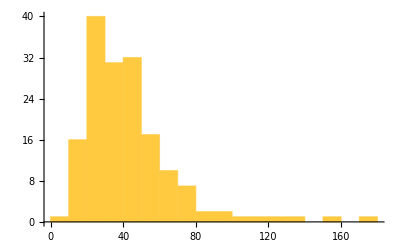

164

```mathematica
Histogram[h=Y[[3]],PlotRange->All]
Length[h]
```

```mathematica
1000*Quantile[h,{0.5,0.75,0.9}]
```

{37565.5,51318.3,70618.}

```mathematica
FindDistribution[h,5]
```

{LogNormalDistribution[3.60902,0.562319],InverseGaussianDistribution[43.3303,114.424],GammaDistribution[3.28552,13.1883],ExtremeValueDistribution[32.4378,17.3025],FrechetDistribution[5.90293,94.2966,-63.421]}

```mathematica
TableForm[SortBy[Map[{DistributionFitTest[h,#,"KolmogorovSmirnov"],#}&,%],-#[[1]]&]]
```

0.967827 | FrechetDistribution[5.90293,94.2966,-63.421]
0.883196 | LogNormalDistribution[3.60902,0.562319]
0.696765 | InverseGaussianDistribution[43.3303,114.424]
0.407291 | ExtremeValueDistribution[32.4378,17.3025]
0.21172 | GammaDistribution[3.28552,13.1883]

```mathematica
Y = Insert[Y,Map[Transpose[Most[#]]&,Y[[5]]],5];
```

```mathematica
Y = SortBy[Transpose[Y],

-#[[4]]&

];
```

```mathematica
Y = Select[Y,(Length[#[[5]]]==6)&];
```

```mathematica
Y = Select[Y,(#[[2]]=="Atmen")&];
```

```mathematica
TableForm[Map[Take[#,4]&,Y]]
Length[Y]
```

Qu19 | Atmen | 33.6512 | 589.182
KP11 | Atmen | 51.3183 | 558.816
KP09 | Atmen | 37.5655 | 455.392
Qu06 | Atmen | 23.4788 | 349.502
KP10 | Atmen | 35.6525 | 296.302
Qu09 | Atmen | 35.8078 | 274.035
KP01 | Atmen | 14.2734 | 227.661
Qu20 | Atmen | 16.1334 | 203.791
Qu16 | Atmen | 24.3656 | 199.528
Qu14 | Atmen | 27.5283 | 180.721
Ob07 | Atmen | 34.5723 | 180.71
Qu11 | Atmen | 33.6173 | 149.265
Qu02 | Atmen | 43.0311 | 119.357
Ob06 | Atmen | 41.2488 | 117.112
Ob04 | Atmen | 43.1666 | 92.9191
Qu18 | Atmen | 41.6495 | 86.0611
Qu01 | Atmen | 26.094 | 48.3343
KP08 | Atmen | 24.1524 | 47.5466
Qu03 | Atmen | 31.2447 | 38.9121
Ob03 | Atmen | 23.3781 | 23.2226
Ob11 | Atmen | 31.4722 | 21.4394
Qu17 | Atmen | 38.6676 | 21.2075
Qu07 | Atmen | 29.552 | -1.14334
Qu04 | Atmen | 54.61 | -2.10241
Qu15 | Atmen | 37.1378 | -10.9664
KP12 | Atmen | 42.7275 | -43.7764
Ob02 | Atmen | 46.2297 | -47.9278
Kl02 | Atmen | 33.4062 | -97.878
KP07 | Atmen | 37.4062 | -104.925
Qu12 | Atmen | 71.7652 | -126.686
Ob10 | Atmen | 28.4054 | -143.527
Ob09 | Atmen | 41.5636 | -145.375
Ob12 | Atmen | 37.2829 | -149.803
KP03 | Atmen | 41.1685 | -156.723
Ob08 | Atmen | 41.4787 | -187.487
KP02 | Atmen | 50.8557 | -194.013
KP06 | Atmen | 52.5747 | -199.218
Qu10 | Atmen | 53.6417 | -304.055
KP04 | Atmen | 58.6368 | -320.352
Ob05 | Atmen | 46.2229 | -343.156
KP05 | Atmen | 71.16 | -393.512
Qu05 | Atmen | 59.8886 | -408.722
Qu13 | Atmen | 42.7595 | -508.348
Tr01 | Atmen | 69.9078 | -597.067

44

```mathematica
Y = Select[Y,MemberQ[{
"Kl02","KP01","KP02","KP04","KP07","KP08","KP10","KP12","Ob02","Ob03","Ob04","Ob05","Ob06","Ob07","Ob09","Ob10","Ob11","Ob12","Qu01","Qu02","Qu03","Qu04","Qu06","Qu07","Qu10","Qu12","Qu14","Qu15","Qu16","Qu17","Qu18","Qu20"
},#[[1]]]&];
Length[Y]
```

32

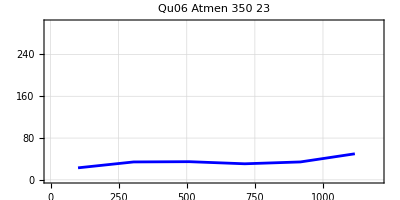
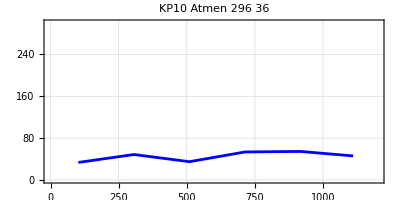
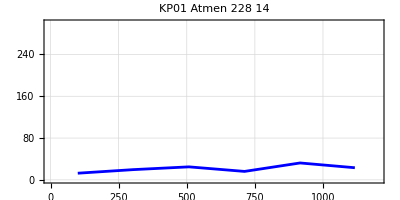
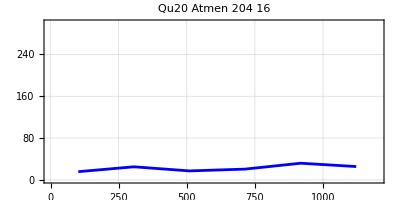
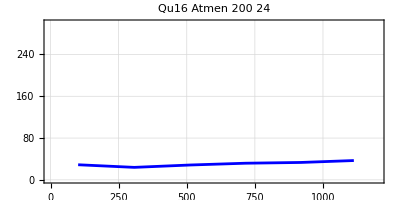
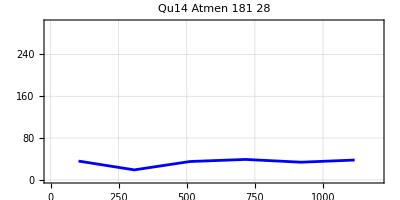
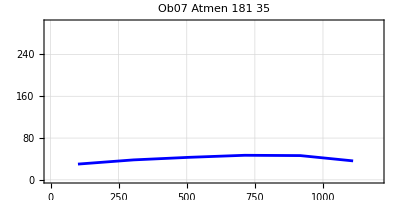
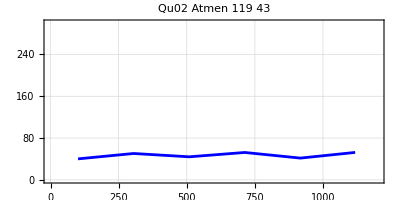

```mathematica
Map[
Graphics[
{Blue,Thickness[0.005],Line[#[[5]]]},
Frame->True,
GridLines->Automatic,
ImageSize->400,
PlotRange->{{0,1200},{0,300}},
PlotLabel->StringJoin[#[[1]],"    ",#[[2]],RealForm[#[[4]],8,0],RealForm[#[[3]],8,0]]
]&,Y]
```

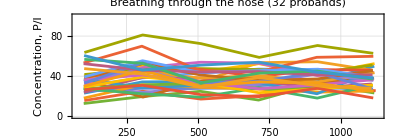

```mathematica
ListLinePlot[Map[#[[5]]&,Y],
AspectRatio->0.35,
Axes->False,
DisplayFunction->Identity,
Frame->True,
FrameLabel->{"Time,  s","Concentration,  P/l"},
GridLines->Automatic,
ImageSize->{Automatic,500},
LabelStyle->MyTS,
PlotLabel->StringJoin["Breathing through the nose  (",ToString[Length[Y]]," probands)"],
PlotRange->{{80,1130},{0,100}}]
```

```mathematica
Clear[f,i];
i = 0;
f = Map[(Clear[a,h,m,n,v,x,y,χ2];
++i;
{x,y,v} = #[[6]];
(*
v *= 10^6;
x /= 3600;
y *= 1000;
*)
n = Length[x];
h = Mean[y];
χ2 = Total[(m-y)^2/v ];
χ2 = FindMinimum[χ2,{m,h}];
Join[
{m/.χ2[[2]],
1-CDF[ChiSquareDistribution[n-2],χ2[[1]]]},
Take[#,2]])&,
Y]
Length[f]
```

{{33.7536,0.070669,Qu06,Atmen},{44.3233,0.0551615,KP10,Atmen},{21.0024,0.154312,KP01,Atmen},{22.2231,0.289253,Qu20,Atmen},{30.2678,0.639929,Qu16,Atmen},{32.9041,0.120426,Qu14,Atmen},{39.9122,0.282506,Ob07,Atmen},{46.6339,0.519963,Qu02,Atmen},{44.7546,0.106066,Ob06,Atmen},{45.9296,0.87931,Ob04,Atmen},{44.2218,0.399629,Qu18,Atmen},{27.5338,0.994522,Qu01,Atmen},{25.576,0.575959,KP08,Atmen},{32.4083,0.375038,Qu03,Atmen},{24.0745,0.43203,Ob03,Atmen},{32.1162,0.149755,Ob11,Atmen},{39.3152,0.773248,Qu17,Atmen},{29.5175,0.954734,Qu07,Atmen},{54.5464,0.0584468,Qu04,Atmen},{36.8053,0.325318,Qu15,Atmen},{41.3985,0.36829,KP12,Atmen},{44.7808,0.443569,Ob02,Atmen},{30.4249,0.446084,Kl02,Atmen},{34.1916,0.605647,KP07,Atmen},{67.8993,0.220776,Qu12,Atmen},{23.9913,0.499003,Ob10,Atmen},{37.0945,0.0506278,Ob09,Atmen},{32.6803,0.214947,Ob12,Atmen},{44.8812,0.784767,KP02,Atmen},{44.2266,0.0685627,Qu10,Atmen},{48.6392,0.170331,KP04,Atmen},{35.571,0.116145,Ob05,Atmen}}

32

```mathematica
MinMax[Map[#[[2]]&,f]]
```

{0.0506278,0.994522}

```mathematica
f = Select[f,(#[[2]]>0.05)&];
Length[f]
```

32

```mathematica
f = SortBy[f,First]
```

{{21.0024,0.154312,KP01,Atmen},{22.2231,0.289253,Qu20,Atmen},{23.9913,0.499003,Ob10,Atmen},{24.0745,0.43203,Ob03,Atmen},{25.576,0.575959,KP08,Atmen},{27.5338,0.994522,Qu01,Atmen},{29.5175,0.954734,Qu07,Atmen},{30.2678,0.639929,Qu16,Atmen},{30.4249,0.446084,Kl02,Atmen},{32.1162,0.149755,Ob11,Atmen},{32.4083,0.375038,Qu03,Atmen},{32.6803,0.214947,Ob12,Atmen},{32.9041,0.120426,Qu14,Atmen},{33.7536,0.070669,Qu06,Atmen},{34.1916,0.605647,KP07,Atmen},{35.571,0.116145,Ob05,Atmen},{36.8053,0.325318,Qu15,Atmen},{37.0945,0.0506278,Ob09,Atmen},{39.3152,0.773248,Qu17,Atmen},{39.9122,0.282506,Ob07,Atmen},{41.3985,0.36829,KP12,Atmen},{44.2218,0.399629,Qu18,Atmen},{44.2266,0.0685627,Qu10,Atmen},{44.3233,0.0551615,KP10,Atmen},{44.7546,0.106066,Ob06,Atmen},{44.7808,0.443569,Ob02,Atmen},{44.8812,0.784767,KP02,Atmen},{45.9296,0.87931,Ob04,Atmen},{46.6339,0.519963,Qu02,Atmen},{48.6392,0.170331,KP04,Atmen},{54.5464,0.0584468,Qu04,Atmen},{67.8993,0.220776,Qu12,Atmen}}

```mathematica
TableForm[f]
```

21.0024 | 0.154312 | KP01 | Atmen
22.2231 | 0.289253 | Qu20 | Atmen
23.9913 | 0.499003 | Ob10 | Atmen
24.0745 | 0.43203 | Ob03 | Atmen
25.576 | 0.575959 | KP08 | Atmen
27.5338 | 0.994522 | Qu01 | Atmen
29.5175 | 0.954734 | Qu07 | Atmen
30.2678 | 0.639929 | Qu16 | Atmen
30.4249 | 0.446084 | Kl02 | Atmen
32.1162 | 0.149755 | Ob11 | Atmen
32.4083 | 0.375038 | Qu03 | Atmen
32.6803 | 0.214947 | Ob12 | Atmen
32.9041 | 0.120426 | Qu14 | Atmen
33.7536 | 0.070669 | Qu06 | Atmen
34.1916 | 0.605647 | KP07 | Atmen
35.571 | 0.116145 | Ob05 | Atmen
36.8053 | 0.325318 | Qu15 | Atmen
37.0945 | 0.0506278 | Ob09 | Atmen
39.3152 | 0.773248 | Qu17 | Atmen
39.9122 | 0.282506 | Ob07 | Atmen
41.3985 | 0.36829 | KP12 | Atmen
44.2218 | 0.399629 | Qu18 | Atmen
44.2266 | 0.0685627 | Qu10 | Atmen
44.3233 | 0.0551615 | KP10 | Atmen
44.7546 | 0.106066 | Ob06 | Atmen
44.7808 | 0.443569 | Ob02 | Atmen
44.8812 | 0.784767 | KP02 | Atmen
45.9296 | 0.87931 | Ob04 | Atmen
46.6339 | 0.519963 | Qu02 | Atmen
48.6392 | 0.170331 | KP04 | Atmen
54.5464 | 0.0584468 | Qu04 | Atmen
67.8993 | 0.220776 | Qu12 | Atmen

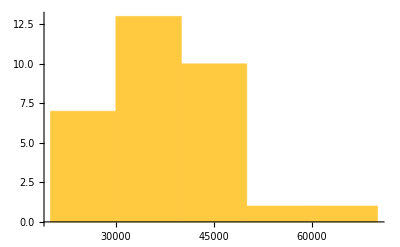

```mathematica
Histogram[h=1000*First/@f]
```

```mathematica
Quantile[h,{0.5,0.75,0.9}]
```

{35571.,44323.3,46633.9}

```mathematica
FindDistribution[h,5]
```

{NormalDistribution[37720.6,11393.8],GammaDistribution[11.5509,3265.59],MixtureDistribution[{0.3632,0.6368},{UniformDistribution[{21002.4,67899.3}],NormalDistribution[35863.8,7755.84]}],LogNormalDistribution[10.4941,0.296076],ExtremeValueDistribution[32515.7,9017.27]}

```mathematica
TableForm[SortBy[Map[{DistributionFitTest[h,#,"KolmogorovSmirnov"],#}&,%],-#[[1]]&]]
```

0.876029 | LogNormalDistribution[10.4941,0.296076]
0.837648 | ExtremeValueDistribution[32515.7,9017.27]
0.831044 | GammaDistribution[11.5509,3265.59]
0.670366 | NormalDistribution[37720.6,11393.8]
0.668538 | MixtureDistribution[{0.3632,0.6368},{UniformDistribution[{21002.4,67899.3}],NormalDistribution[35863.8,7755.84]}]

```mathematica
distc0 = LogNormalDistribution[10.494050849748307,0.2960755285049445]
```

LogNormalDistribution[10.4941,0.296076]

```mathematica
Join[Quartiles[distc0],{Mean[distc0],Quantile[distc0,0.95]}]
```

{29565.1,36100.1,44079.5,37717.6,58750.3}

```mathematica
Clear[a,b,c,x,y,W]
W = Import["https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/2020_aerosol-wind-instruments/particle-emission-rate-from-breathing_Reichert_et_al.xlsx"][[1]];
W = Select[W,(#[[4]]==="0,3 – 5 μm")&];
TableForm[W]
W = Map[Drop[#,4]&,W];
W = Map[(First[#]->Select[Rest[#],NumericQ])&,W];
Column[W]
W = {"Ruheatmung Nase","Ruheatmung Mund"}/.W;
W = SortBy[Transpose[W],First]
```

0. | 25.1276 | 741.264 | 0,3 – 5 μm | Ruheatmung Nase | 343.934 | 62.819 | 10.9933 | 7.85238 | 1.57048 | 34.5505 | 26.6981 | 15.7048 | 172.752 | 130.349 | 6.2819 | 15.7048 | 0. | 43.9733 | 741.264 | 108.363 | 23.5571 | 1.57048 | 53.3962 | 9.42285 | 
1.57048 | 64.3895 | 1036.51 | 0,3 – 5 μm | Ruheatmung Mund | 1036.51 | 452.297 | 1.57048 | 69.1009 | 9.42285 | 76.9533 | 430.31 | 6.2819 | 733.412 | 581.076 | 25.1276 | 59.6781 | 1.57048 | 58.1076 | 683.157 | 58.1076 | 78.5238 | 3.14095 | 138.202 | 15.7048 |

Ruheatmung Nase→{343.934,62.819,10.9933,7.85238,1.57048,34.5505,26.6981,15.7048,172.752,130.349,6.2819,15.7048,0.,43.9733,741.264,108.363,23.5571,1.57048,53.3962,9.42285}
Ruheatmung Mund→{1036.51,452.297,1.57048,69.1009,9.42285,76.9533,430.31,6.2819,733.412,581.076,25.1276,59.6781,1.57048,58.1076,683.157,58.1076,78.5238,3.14095,138.202,15.7048}

{{0.,1.57048},{1.57048,3.14095},{1.57048,9.42285},{6.2819,25.1276},{7.85238,69.1009},{9.42285,15.7048},{10.9933,1.57048},{15.7048,6.2819},{15.7048,59.6781},{23.5571,78.5238},{26.6981,430.31},{34.5505,76.9533},{43.9733,58.1076},{53.3962,138.202},{62.819,452.297},{108.363,58.1076},{130.349,581.076},{172.752,733.412},{343.934,1036.51},{741.264,683.157}}

```mathematica
W = Take[W,{2,-2}]
```

{{1.57048,3.14095},{1.57048,9.42285},{6.2819,25.1276},{7.85238,69.1009},{9.42285,15.7048},{10.9933,1.57048},{15.7048,6.2819},{15.7048,59.6781},{23.5571,78.5238},{26.6981,430.31},{34.5505,76.9533},{43.9733,58.1076},{53.3962,138.202},{62.819,452.297},{108.363,58.1076},{130.349,581.076},{172.752,733.412},{343.934,1036.51}}

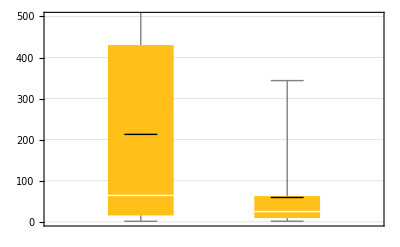

```mathematica
BoxWhiskerChart[
Reverse[Transpose[W]],
"Mean",
GridLines->Automatic,
PlotRange->{0,500}]
```

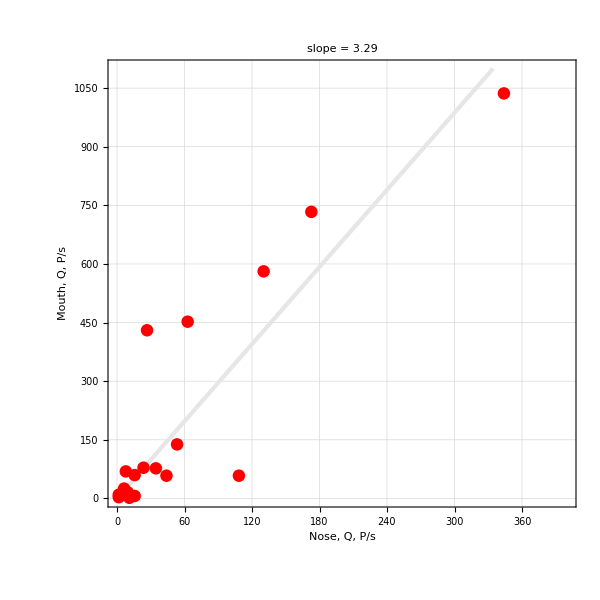

```mathematica
Graphics[
{GrayLevel[0.9],Thickness[0.005],
Line[{y/(c=Coefficient[Fit[W,{x},x],x]),y}/.List/@{y->0,y->1100}],
Red,PointSize[0.015],Point[W]},
AspectRatio->1,
Axes->False,
Frame->True,
FrameLabel->{"Nose, Q, P/s","Mouth, Q, P/s"},
GridLines->Automatic,
ImageSize->600,
LabelStyle->MyTS,
PlotLabel->StringJoin["slope = ",RealForm[c,4,2]],
PlotRange->{{0,400},{0,1100}}]
```

```mathematica
{a,b} = Transpose[W];
Correlation[a,b]
```

0.887473

```mathematica
FindDistribution[a,5]
```

{LogNormalDistribution[3.18568,1.61626],WeibullDistribution[0.684046,53.6296],GammaDistribution[0.578653,122.275],ExponentialDistribution[0.0141333],MixtureDistribution[{0.773707,0.226293},{ExponentialDistribution[0.0392502],NormalDistribution[225.561,109.696]}]}

```mathematica
TableForm[SortBy[Map[{DistributionFitTest[a,#(*,"KolmogorovSmirnov"*)],#}&,%],-#[[1]]&]]
```

0.995182 | LogNormalDistribution[3.18568,1.61626]
0.995182 | WeibullDistribution[0.684046,53.6296]
0.963099 | GammaDistribution[0.578653,122.275]
0.808847 | MixtureDistribution[{0.773707,0.226293},{ExponentialDistribution[0.0392502],NormalDistribution[225.561,109.696]}]
0.60194 | ExponentialDistribution[0.0141333]

```mathematica
distQ = TransformedDistribution[3600*x,x\[Distributed]LogNormalDistribution[3.1856844191743607,1.61626483599928]]
```

LogNormalDistribution[11.3744,1.61626]

```mathematica
Join[Quartiles[distQ],{Mean[distQ],Quantile[distQ,0.95]}]
```

{29267.1,87061.8,258986.,321428.,1.24282×10^6}

```mathematica
%/3600
```

{8.12975,24.1838,71.9404,89.2856,345.227}

```mathematica
distQ
distc0
```

LogNormalDistribution[11.3744,1.61626]

LogNormalDistribution[10.4941,0.296076]

```mathematica
μ = distQ[[1]]-distc0[[1]]-Log[QubusVolume]
μ = Exp[μ]
```

-2.1104

0.12119

```mathematica
μ = 87000/36000/QubusVolume
```

0.121441

```mathematica
Clear[c0,cs,h,Q,q,R,t,V,λ]

h = ((1-ⅇ^(- λ t))/(λ t) (1-c0/cs))/.(cs->Q/(λ V) );

ExpressionVariables[h]
```

{c0,Q,t,V,λ}

```mathematica
FullSimplify[((ⅇ^(-t λ) (-1+ⅇ^(t λ)) (Q-c0 V λ))/(t V λ))/(Q/V)/h]
```

1

```mathematica
R = {
c0->50000,
t  ->1/3,
V  ->QubusVolume,
λ  ->0.121}
```

{c0→50000,t→1/3,V→19.9,λ→0.121}

```mathematica
h = h/.%;
ExpressionVariables[h]
```

{Q}

```mathematica
h = FullSimplify[h,Assumptions->{α>0,Q>0}]
```

0.980102-117999./Q

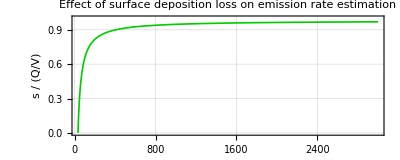

```mathematica
Plot[h/.Q->3600*q,{q,0,3000},
AspectRatio->0.4,
Axes->False,
DisplayFunction->Identity,
Frame->True,
FrameLabel->{"Q,  P/s","s / (Q/V)"},
GridLines->Automatic,
ImageSize->{Automatic,500},
LabelStyle->MyTS,
PlotLabel->"Effect of surface deposition loss on emission rate estimation",
PlotRange->{All,{0,1}},
PlotStyle->{{RGBColor[0,0.8,0],Thickness[0.003]}}]
```

```mathematica
Solve[(h/.Q->3600*q)==0.8,q]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{q→181.995}}

```mathematica
(cs->Q/(λ V) )/.R
```

cs→0.4153 Q

```mathematica
(c0/.R)/((cs/Q)/.%)
```

120395.

```mathematica
%/3600
```

33.4431